```mathematica
<< "/Users/raina/Documents/MathematicaNB/Dynamica1.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
lineThickness=0.012;
legendThickness=lineThickness*20;
labelSize=20;
tickSize=15;
legendSize=15;
textSize=20;
colours=ColorData[97,"ColorList"];
```

```mathematica
Clear[Ad,Bd,Ae,Be,n,qa,qb,tu,td,te]
ϵ=10^-5;
sysCI2EqNnewants1n=DynamicalSystem[{
-(Ad(1-n))/(qa td) -(Ad n)/(qa td)   + Ae/te ,
-(Bd(1-n))/(qb td)-(Bd n)/(qb td) +Be/te   ,
+Ad((1-n)/(qa td))(Ad/(Ad+Bd) ) +(Ad/(Ad+Bd) )((1-Ad-Ae-Bd-Be)(1-n))/tu+  Ad((n)/(qa td))(Bd/(Ad+Bd) )+ (1-Ad-Bd-Ae-Be)((n)/tu) (Bd/(Ad+Bd) )- Ae/te ,
+Bd((1-n)/(qb td))(Bd/(Ad+Bd) ) +(Bd/(Ad+Bd) )((1-Ad-Ae-Bd-Be)(1-n))/tu+  Bd((n)/(qb td))(Ad/(Ad+Bd) )+ (1-Ad-Bd-Ae-Be)((n)/tu) (Ad/(Ad+Bd) )- Be/te
 },
{{Ad,-0.01,1+0.01},{Bd,-0.01,1+0.01},{Ae,-0.01,1+0.01},{Be,-0.01,1+0.01}},
{{tu,ϵ,5000},{te,ϵ,5000},{td,ϵ,5000},{qa,ϵ,1},{qb,ϵ,1},{n,0,1}}]
```

DynamicalSystem[«4 ODEs»,{Ad,Bd,Ae,Be},{tu,te,td,qa,qb,n}]

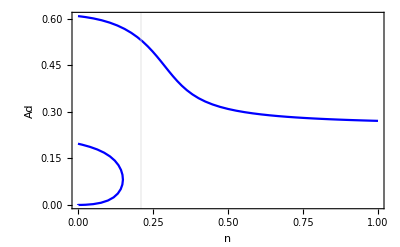

```mathematica
DisplayBifurcationDiagram[sysCI2EqNnewants1n/.{tu->80,te->180,td->280,qa->1,qb->0.66},
n,StateVariables->{Ad},GridLines->{{0.21},{0.7}}]
```

```mathematica
Clear[Ad,Bd,Ae,Be,n,qa,qb]
td=280;
te=1;
tu=80;
qa=1;

sysCI2EqNnewants1nsol1={
-(Ad(1-n))/(qa td) -(Ad n)/(qa td)   + Ae/te ,
-(Bd(1-n))/(qb td)-(Bd n)/(qb td) +Be/te   ,
+Ad((1-n)/(qa td))(Ad/(Ad+Bd) ) +(Ad/(Ad+Bd) )((1-Ad-Ae-Bd-Be)(1-n))/tu+  Ad((n)/(qa td))(Bd/(Ad+Bd) )+ (1-Ad-Bd-Ae-Be)((n)/tu) (Bd/(Ad+Bd) )- Ae/te ,
+Bd((1-n)/(qb td))(Bd/(Ad+Bd) ) +(Bd/(Ad+Bd) )((1-Ad-Ae-Bd-Be)(1-n))/tu+  Bd((n)/(qb td))(Ad/(Ad+Bd) )+ (1-Ad-Bd-Ae-Be)((n)/tu) (Ad/(Ad+Bd) )- Be/te
}
simple=False;
fixedPointsCInoiseSymGsol1=If[simple,Simplify[Solve[{sysCI2EqNnewants1nsol1==0},{Ad,Bd,Ae,Be}]],Solve[{sysCI2EqNnewants1nsol1==0},{Ad,Bd,Ae,Be}]]
"Found "<>ToString[Length[fixedPointsCInoiseSymGsol1]]<>" fixed points"
```

{Ae-1/280 Ad (1-n)-(Ad n)/280,Be-(Bd (1-n))/(280 qb)-(Bd n)/(280 qb),-Ae+(Ad^2 (1-n))/(280 (Ad+Bd))+(Ad (1-Ad-Ae-Bd-Be) (1-n))/(80 (Ad+Bd))+(Ad Bd n)/(280 (Ad+Bd))+(Bd (1-Ad-Ae-Bd-Be) n)/(80 (Ad+Bd)),-Be+(Bd (1-Ad-Ae-Bd-Be) (1-n))/(80 (Ad+Bd))+(Ad (1-Ad-Ae-Bd-Be) n)/(80 (Ad+Bd))+(Bd^2 (1-n))/(280 (Ad+Bd) qb)+(Ad Bd n)/(280 (Ad+Bd) qb)}

{{Ad→(-44060800 qb^2+75577600 n qb^2-31673600 n^2 qb^2-154763560 qb^3+27+173919044 n qb^2 1^2-124191604 n^2 qb^2 (1)^2-44218160 qb^3 ((280 (1))/(3 (1))-1/1+1^1/1)^2+176557920 n qb^3 ((280 (562 qb-964 n qb+405 n^2 qb+7+628881 n^2 qb^3))/(3 (281-482 n+12+88121880 n^2 qb^3))-1/1+(1)^(1/3)/(3 2^1 (15+1)))^2-176243760 n^2 qb^3 ((280 (562 qb-964 n qb+405 n^2 qb+179840 qb^2-467526 n qb^2+221926 n^2 qb^2+78961 qb^3-472642 n qb^3+628881 n^2 qb^3))/(3 (281-482 n+202 n^2+179840 qb+1331436 n qb-1065876 n^2 qb+28403761 qb^2-86959522 n qb^2+62095802 n^2 qb^2+22109080 qb^3-88278960 n qb^3+88121880 n^2 qb^3))-(2^1 1)/1+(1)^(1/3)/(3 2^1 (281-482 n+12+88121880 n^2 qb^3)))^2)/(-44218160 qb^2+63258720 n qb^2-22624560 n^2 qb^2-155316287 qb^3+266414414 n qb^3+44218160 n^2 qb^3),Bd→(280 (562 qb-964 n qb+405 n^2 qb+179840 qb^2-467526 n qb^2+221926 n^2 qb^2+78961 qb^3-472642 n qb^3+628881 n^2 qb^3))/(3 (281-482 n+202 n^2+179840 qb+1331436 n qb-1065876 n^2 qb+28403761 qb^2-86959522 n qb^2+62095802 n^2 qb^2+22109080 qb^3-88278960 n qb^3+88121880 n^2 qb^3))-(2^1 (1))/(3 1 1^1)+(1)^(1/3)/(3 2^1 (281-482 n+12+88121880 n^2 qb^3)),Ae→1,Be→-(-(280 (562 qb-964 n qb+405 n^2 qb+179840 qb^2-467526 n qb^2+221926 n^2 qb^2+78961 qb^3-472642 n qb^3+628881 n^2 qb^3))/(3 (281-482 n+202 n^2+179840 qb+1331436 n qb-1065876 n^2 qb+28403761 qb^2-86959522 n qb^2+62095802 n^2 qb^2+22109080 qb^3-88278960 n qb^3+88121880 n^2 qb^3))+(2^1 1)/(3 (1) 1)-(1)^(1/3)/(3 2^111 (15+88121880 n^2 qb^3)))/(280 qb)},{1},{1}}
 |  |  |  |

Found 3 fixed points

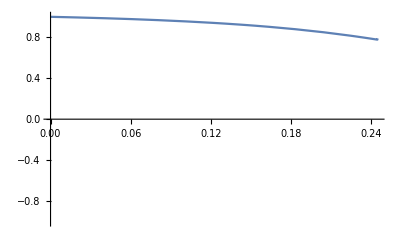

```mathematica
Print[Plot[{fixedPointsCInoiseSymGsol1⟦2,1,2⟧/.{qb->0.75}},{n,0,1},PlotRange->{-1,1},GridLines->{{1/3},{}}]];
```

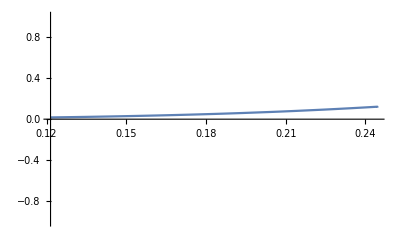

```mathematica
Print[Plot[{fixedPointsCInoiseSymGsol1⟦2,2,2⟧/.{qb->0.75}},{n,0,1},PlotRange->{-1,1},GridLines->{{1/3},{}}]];
```

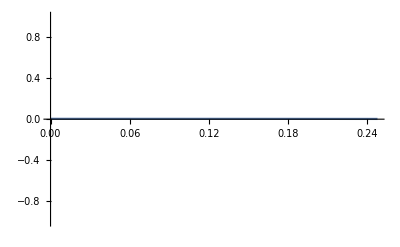

```mathematica
Print[Plot[{fixedPointsCInoiseSymGsol1⟦2,3,2⟧/.{qb->0.9}},{n,0,1},PlotRange->{-1,1},GridLines->{{1/3},{}}]];
```

```mathematica
sol3disapcheck= Solve[((-974143752064000 qb^3+5012853613824000 n qb^3-10688982648960000 n^2 qb^3+12087790650880000 n^3 qb^3-7645855916160000 n^4 qb^3+2564864918784000 n^5 qb^3-356526866304000 n^6 qb^3-935178001981440000 qb^4-50471292604113024000 n qb^4+219055881267538560000 n^2 qb^4-366513243560962176000 n^3 qb^4+302501996075303808000 n^4 qb^4-123746664499008768000 n^5 qb^4+20108197858775040000 n^6 qb^4-285639892195834176000 qb^5-16348654502077720704000 n qb^5+86599788173872632960000 n^2 qb^5-165667882605990481920000 n^3 qb^5+151709125485203244672000 n^4 qb^5-67821486074351455488000 n^5 qb^5+11951186648686411392000 n^6 qb^5-27596128694720230400000 qb^6+89340939141486305280000 n qb^6+41633284651585589760000 n^2 qb^6-355722850352023526400000 n^3 qb^6+270978086574111436800000 n^4 qb^6+30662030649168414720000 n^5 qb^6-54988664936330567680000 n^6 qb^6-8425134055885412544000 qb^7-24520609773747620736000 n qb^7+460257815265707598720000 n^2 qb^7-1333614470342453483520000 n^3 qb^7+1369765000034825186688000 n^4 qb^7-560110965332770182912000 n^5 qb^7+271251094176170656128000 n^6 qb^7+50766780772438832640000 qb^8-328089559277694592896000 n qb^8+1076974936405970797440000 n^2 qb^8-2470270863759217728384000 n^3 qb^8+3298096287440028396672000 n^4 qb^8-1495802484519385658112000 n^5 qb^8-420364546273810575360000 n^6 qb^8+21614341510689866624000 qb^9-194298315501788623104000 n qb^9+711658784395007352960000 n^2 qb^9-1357323216421249441280000 n^3 qb^9+1420784975251242437760000 n^4 qb^9-774429910373962047744000 n^5 qb^9+171993341140060454784000 n^6 qb^9)^2+4 (-78400 (562 qb-964 n qb+405 n^2 qb+179840 qb^2-467526 n qb^2+221926 n^2 qb^2+78961 qb^3-472642 n qb^3+628881 n^2 qb^3)^2+235200 (281 qb^2-482 n qb^2+204 n^2 qb^2-562 n qb^3+1402 n^2 qb^3) (281-482 n+202 n^2+179840 qb+1331436 n qb-1065876 n^2 qb+28403761 qb^2-86959522 n qb^2+62095802 n^2 qb^2+22109080 qb^3-88278960 n qb^3+88121880 n^2 qb^3))^3)==0,n];
```

```mathematica
(*eb =EquilibriumBranches[sysCI2EqNnewants1n/.{tu->800,te->0.001 ,td->1800,qa->1,qb->0.90},n];
eb[[1]];*)
```

```mathematica
bifPintCInoiseViaUAsymc=FullSimplify[sol3disapcheck⟦9⟧⟦1,2⟧]
```

1/4 (((3+qb) (1+3 qb))/(-1+qb)^2-√(((3+qb)^2 (1+3 qb)^2-8 (-1+qb^2)^2+6 2^(1/3) (-1+qb)^2 (-qb (-1+qb^2)^2)^(1/3))/(-1+qb)^4)-√2 √((-8 (-1+qb)^4 (1+qb)^2+(-1+qb)^2 (3+qb)^2 (1+3 qb)^2-3 2^(1/3) (-1+qb)^4 (-qb (-1+qb^2)^2)^(1/3)+((1+qb (6+qb)) (1+qb (-132+qb (-250+(-132+qb) qb))))/(√(1+256/(-1+qb)^4+512/(-1+qb)^3+320/(-1+qb)^2+64/(-1+qb)+(6 2^(1/3) (-qb (-1+qb^2)^2)^(1/3))/(-1+qb)^2)))/(-1+qb)^6))

```mathematica
(*bifPintCInoiseViaUAsymc/.{qb->0.99}*)
```

Found 2 stable branches and 1 saddle branches

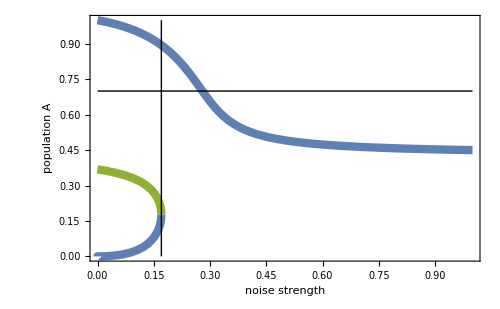

```mathematica
params={tu->80,te->0.01,td->280,qa->1,qb->0.75};
strength=1;
ratio=0.75;
values={nv->strength};
eb=EquilibriumBranches[sysCI2EqNnewants1n/.(params),n];
stableBranches=List[];
saddleBranches=List[];
Do[
If[branch[[2]]==Symbol["Stable"],
AppendTo[stableBranches,branch]];
If[branch[[2]]==Symbol["Saddle"],
AppendTo[saddleBranches,branch]];
,{branch,eb[[1]]}];

Print["Found "<>ToString[Length[stableBranches]]<>" stable branches and "<>ToString[Length[saddleBranches]]<>" saddle branches"]
plt=Show[
ListLinePlot[Table[stableBranches[[sb]][[4]][[All,{5,1}]],{sb,Range[1,Length[stableBranches]]}],PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}]],
ListLinePlot[saddleBranches[[1]][[4]][[All,{5,1}]],PlotStyle->{colours[[3]],Thickness[lineThickness]}],
Graphics[{
Line[{{0,0.7},{1,0.7}}],
Line[{{ Re[bifPintCInoiseViaUAsymc/.{qb->ratio}],0},{Re[bifPintCInoiseViaUAsymc/.{qb->ratio}],1}}]
}],
PlotRange->{0,1},ImageSize->500,Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
FrameLabel->{"noise strength","population A"}
]
```